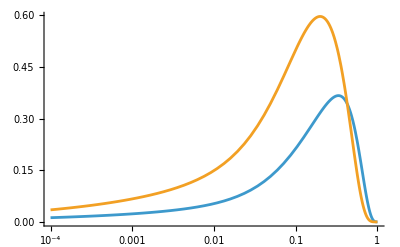

```mathematica
adg[4]=0;


x=.
aug[1]=-0.270136442453640;
aug[2]=0.04597870221194073;
aug[3]=-0.004409042268511016;
avu=0.271805383383747;
bvu=5.64529939736921;
bvd=-1.88794945187232;
lan=0.317366895984001;

aaa =2/((Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(7 aug[1] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(28 aug[2] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(84 aug[3] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]-(14 aug[1] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]-(126 aug[2] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]-(630 aug[3] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]+(126 aug[2] Gamma[2+avu] Gamma[1+bvu])/Gamma[3+avu+bvu]+(1386 aug[3] Gamma[2+avu] Gamma[1+bvu])/Gamma[3+avu+bvu]-(924 aug[3] Gamma[3+avu] Gamma[1+bvu])/Gamma[4+avu+bvu]);
xuvgegn=aaa x^avu(1-x)^bvu(1+∑_(i=1)^3 aug[i]GegenbauerC[i,7/2,1-2x]);


bbb=1/ ((Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(7 aug[1] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(28 aug[2] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(84 aug[3] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]-(14 aug[1] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]-(126 aug[2] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]-(630 aug[3] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]+(126 aug[2] Gamma[2+avu] Gamma[1+bvd+bvu])/Gamma[3+avu+bvd+bvu]+(1386 aug[3] Gamma[2+avu] Gamma[1+bvd+bvu])/Gamma[3+avu+bvd+bvu]-(924 aug[3] Gamma[3+avu] Gamma[1+bvd+bvu])/Gamma[4+avu+bvd+bvu]);


xdvgegen=bbb x^avu(1-x)^bvu(1-x)^bvd(1+∑_(i=1)^3 aug[i]GegenbauerC[i,7/2,1-2x]);

LogLinearPlot[{xdvgegen,xuvgegn},{x,0.0001,1}]
```

```mathematica
Dn=(15 ((0.9275618053002308 Gamma[1+bvu] Gamma[avu+s])/Gamma[1+avu+bvu+s]+(6.492932637101616 aug[1] Gamma[1+bvu] Gamma[avu+s])/Gamma[1+avu+bvu+s]+(25.971730548406462 aug[2] Gamma[1+bvu] Gamma[avu+s])/Gamma[1+avu+bvu+s]+(77.91519164521938 aug[3] Gamma[1+bvu] Gamma[avu+s])/Gamma[1+avu+bvu+s]+(1.5413863209114538 Gamma[1+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvu+s]-(2.196161027823054 aug[1] Gamma[1+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvu+s]-(73.71397048230838 aug[2] Gamma[1+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvu+s]-(454.8874863825833 aug[3] Gamma[1+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvu+s]-(5.109405666082289 Gamma[1+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvu+s]-(57.34524815533638 aug[1] Gamma[1+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvu+s]-(220.4052476173182 aug[2] Gamma[1+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvu+s]-(114.66279597900825 aug[3] Gamma[1+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvu+s]+(4.064017965930289 Gamma[1+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvu+s]+(99.97980508666407 aug[1] Gamma[1+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvu+s]+(951.7922934072598 aug[2] Gamma[1+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvu+s]+(4839.597411455848 aug[3] Gamma[1+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvu+s]-(56.89625152302404 aug[1] Gamma[1+bvu] Gamma[4+avu+s])/Gamma[5+avu+bvu+s]-(1155.851377633585 aug[2] Gamma[1+bvu] Gamma[4+avu+s])/Gamma[5+avu+bvu+s]-(11066.208532248318 aug[3] Gamma[1+bvu] Gamma[4+avu+s])/Gamma[5+avu+bvu+s]+(512.0662637072164 aug[2] Gamma[1+bvu] Gamma[5+avu+s])/Gamma[6+avu+bvu+s]+(10353.819736239415 aug[3] Gamma[1+bvu] Gamma[5+avu+s])/Gamma[6+avu+bvu+s]-(3755.1526005195874 aug[3] Gamma[1+bvu] Gamma[6+avu+s])/Gamma[7+avu+bvu+s]))/(14 ((Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(7 aug[1] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(28 aug[2] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(84 aug[3] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]-(14 aug[1] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]-(126 aug[2] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]-(630 aug[3] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]+(126 aug[2] Gamma[2+avu] Gamma[1+bvu])/Gamma[3+avu+bvu]+(1386 aug[3] Gamma[2+avu] Gamma[1+bvu])/Gamma[3+avu+bvu]-(924 aug[3] Gamma[3+avu] Gamma[1+bvu])/Gamma[4+avu+bvu]))+(13 ((0.9275618053002308 Gamma[1+bvd+bvu] Gamma[avu+s])/Gamma[1+avu+bvd+bvu+s]+(6.492932637101616 aug[1] Gamma[1+bvd+bvu] Gamma[avu+s])/Gamma[1+avu+bvd+bvu+s]+(25.971730548406462 aug[2] Gamma[1+bvd+bvu] Gamma[avu+s])/Gamma[1+avu+bvd+bvu+s]+(77.91519164521938 aug[3] Gamma[1+bvd+bvu] Gamma[avu+s])/Gamma[1+avu+bvd+bvu+s]+(1.5413863209114538 Gamma[1+bvd+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvd+bvu+s]-(2.196161027823054 aug[1] Gamma[1+bvd+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvd+bvu+s]-(73.71397048230838 aug[2] Gamma[1+bvd+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvd+bvu+s]-(454.8874863825833 aug[3] Gamma[1+bvd+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvd+bvu+s]-(5.109405666082289 Gamma[1+bvd+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvd+bvu+s]-(57.34524815533638 aug[1] Gamma[1+bvd+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvd+bvu+s]-(220.4052476173182 aug[2] Gamma[1+bvd+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvd+bvu+s]-(114.66279597900825 aug[3] Gamma[1+bvd+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvd+bvu+s]+(4.064017965930289 Gamma[1+bvd+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvd+bvu+s]+(99.97980508666407 aug[1] Gamma[1+bvd+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvd+bvu+s]+(951.7922934072598 aug[2] Gamma[1+bvd+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvd+bvu+s]+(4839.597411455848 aug[3] Gamma[1+bvd+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvd+bvu+s]-(56.89625152302404 aug[1] Gamma[1+bvd+bvu] Gamma[4+avu+s])/Gamma[5+avu+bvd+bvu+s]-(1155.851377633585 aug[2] Gamma[1+bvd+bvu] Gamma[4+avu+s])/Gamma[5+avu+bvd+bvu+s]-(11066.208532248318 aug[3] Gamma[1+bvd+bvu] Gamma[4+avu+s])/Gamma[5+avu+bvd+bvu+s]+(512.0662637072164 aug[2] Gamma[1+bvd+bvu] Gamma[5+avu+s])/Gamma[6+avu+bvd+bvu+s]+(10353.819736239415 aug[3] Gamma[1+bvd+bvu] Gamma[5+avu+s])/Gamma[6+avu+bvd+bvu+s]-(3755.1526005195874 aug[3] Gamma[1+bvd+bvu] Gamma[6+avu+s])/Gamma[7+avu+bvd+bvu+s]))/(28 ((Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(7 aug[1] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(28 aug[2] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(84 aug[3] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]-(14 aug[1] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]-(126 aug[2] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]-(630 aug[3] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]+(126 aug[2] Gamma[2+avu] Gamma[1+bvd+bvu])/Gamma[3+avu+bvd+bvu]+(1386 aug[3] Gamma[2+avu] Gamma[1+bvd+bvu])/Gamma[3+avu+bvd+bvu]-(924 aug[3] Gamma[3+avu] Gamma[1+bvd+bvu])/Gamma[4+avu+bvd+bvu]));


Un=(13 (-(0.07232232765081216 Gamma[0.6+bvu] Gamma[avu+s])/Gamma[0.6000000000000001+avu+bvu+s]-(0.5062562935556851 aug[1] Gamma[0.6+bvu] Gamma[avu+s])/Gamma[0.6000000000000001+avu+bvu+s]-(2.0250251742227405 aug[2] Gamma[0.6+bvu] Gamma[avu+s])/Gamma[0.6000000000000001+avu+bvu+s]-(6.075075522668222 aug[3] Gamma[0.6+bvu] Gamma[avu+s])/Gamma[0.6000000000000001+avu+bvu+s]+(Gamma[1+bvu] Gamma[avu+s])/Gamma[1+avu+bvu+s]+(7 aug[1] Gamma[1+bvu] Gamma[avu+s])/Gamma[1+avu+bvu+s]+(28 aug[2] Gamma[1+bvu] Gamma[avu+s])/Gamma[1+avu+bvu+s]+(84 aug[3] Gamma[1+bvu] Gamma[avu+s])/Gamma[1+avu+bvu+s]+(1.5413863209114538 Gamma[0.6+bvu] Gamma[1+avu+s])/Gamma[1.6+avu+bvu+s]+(11.802216833491546 aug[1] Gamma[0.6+bvu] Gamma[1+avu+s])/Gamma[1.6+avu+bvu+s]+(52.27143026952304 aug[2] Gamma[0.6+bvu] Gamma[1+avu+s])/Gamma[1.6+avu+bvu+s]+(175.03951737657377 aug[3] Gamma[0.6+bvu] Gamma[1+avu+s])/Gamma[1.6+avu+bvu+s]-(14 aug[1] Gamma[1+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvu+s]-(126 aug[2] Gamma[1+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvu+s]-(630 aug[3] Gamma[1+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvu+s]-(5.109405666082289 Gamma[0.6+bvu] Gamma[2+avu+s])/Gamma[2.6+avu+bvu+s]-(57.34524815533638 aug[1] Gamma[0.6+bvu] Gamma[2+avu+s])/Gamma[2.6+avu+bvu+s]-(346.39064836914963 aug[2] Gamma[0.6+bvu] Gamma[2+avu+s])/Gamma[2.6+avu+bvu+s]-(1500.5022042491537 aug[3] Gamma[0.6+bvu] Gamma[2+avu+s])/Gamma[2.6+avu+bvu+s]+(126 aug[2] Gamma[1+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvu+s]+(1386 aug[3] Gamma[1+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvu+s]+(4.064017965930289 Gamma[0.6+bvu] Gamma[3+avu+s])/Gamma[3.6+avu+bvu+s]+(99.97980508666407 aug[1] Gamma[0.6+bvu] Gamma[3+avu+s])/Gamma[3.6+avu+bvu+s]+(951.7922934072598 aug[2] Gamma[0.6+bvu] Gamma[3+avu+s])/Gamma[3.6+avu+bvu+s]+(5763.490350302612 aug[3] Gamma[0.6+bvu] Gamma[3+avu+s])/Gamma[3.6+avu+bvu+s]-(924 aug[3] Gamma[1+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvu+s]-(56.89625152302404 aug[1] Gamma[0.6+bvu] Gamma[4+avu+s])/Gamma[4.6+avu+bvu+s]-(1155.851377633585 aug[2] Gamma[0.6+bvu] Gamma[4+avu+s])/Gamma[4.6+avu+bvu+s]-(11066.208532248318 aug[3] Gamma[0.6+bvu] Gamma[4+avu+s])/Gamma[4.6+avu+bvu+s]+(512.0662637072164 aug[2] Gamma[0.6+bvu] Gamma[5+avu+s])/Gamma[5.6+avu+bvu+s]+(10353.819736239415 aug[3] Gamma[0.6+bvu] Gamma[5+avu+s])/Gamma[5.6+avu+bvu+s]-(3755.1526005195874 aug[3] Gamma[0.6+bvu] Gamma[6+avu+s])/Gamma[6.6+avu+bvu+s]))/(14 ((Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(7 aug[1] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(28 aug[2] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(84 aug[3] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]-(14 aug[1] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]-(126 aug[2] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]-(630 aug[3] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]+(126 aug[2] Gamma[2+avu] Gamma[1+bvu])/Gamma[3+avu+bvu]+(1386 aug[3] Gamma[2+avu] Gamma[1+bvu])/Gamma[3+avu+bvu]-(924 aug[3] Gamma[3+avu] Gamma[1+bvu])/Gamma[4+avu+bvu]))+(15 (-(0.07232232765081216 Gamma[0.6+bvd+bvu] Gamma[avu+s])/Gamma[0.6000000000000001+avu+bvd+bvu+s]-(0.5062562935556851 aug[1] Gamma[0.6+bvd+bvu] Gamma[avu+s])/Gamma[0.6000000000000001+avu+bvd+bvu+s]-(2.0250251742227405 aug[2] Gamma[0.6+bvd+bvu] Gamma[avu+s])/Gamma[0.6000000000000001+avu+bvd+bvu+s]-(6.075075522668222 aug[3] Gamma[0.6+bvd+bvu] Gamma[avu+s])/Gamma[0.6000000000000001+avu+bvd+bvu+s]+(Gamma[1+bvd+bvu] Gamma[avu+s])/Gamma[1+avu+bvd+bvu+s]+(7 aug[1] Gamma[1+bvd+bvu] Gamma[avu+s])/Gamma[1+avu+bvd+bvu+s]+(28 aug[2] Gamma[1+bvd+bvu] Gamma[avu+s])/Gamma[1+avu+bvd+bvu+s]+(84 aug[3] Gamma[1+bvd+bvu] Gamma[avu+s])/Gamma[1+avu+bvd+bvu+s]+(1.5413863209114538 Gamma[0.6+bvd+bvu] Gamma[1+avu+s])/Gamma[1.6+avu+bvd+bvu+s]+(11.802216833491546 aug[1] Gamma[0.6+bvd+bvu] Gamma[1+avu+s])/Gamma[1.6+avu+bvd+bvu+s]+(52.27143026952304 aug[2] Gamma[0.6+bvd+bvu] Gamma[1+avu+s])/Gamma[1.6+avu+bvd+bvu+s]+(175.03951737657377 aug[3] Gamma[0.6+bvd+bvu] Gamma[1+avu+s])/Gamma[1.6+avu+bvd+bvu+s]-(14 aug[1] Gamma[1+bvd+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvd+bvu+s]-(126 aug[2] Gamma[1+bvd+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvd+bvu+s]-(630 aug[3] Gamma[1+bvd+bvu] Gamma[1+avu+s])/Gamma[2+avu+bvd+bvu+s]-(5.109405666082289 Gamma[0.6+bvd+bvu] Gamma[2+avu+s])/Gamma[2.6+avu+bvd+bvu+s]-(57.34524815533638 aug[1] Gamma[0.6+bvd+bvu] Gamma[2+avu+s])/Gamma[2.6+avu+bvd+bvu+s]-(346.39064836914963 aug[2] Gamma[0.6+bvd+bvu] Gamma[2+avu+s])/Gamma[2.6+avu+bvd+bvu+s]-(1500.5022042491537 aug[3] Gamma[0.6+bvd+bvu] Gamma[2+avu+s])/Gamma[2.6+avu+bvd+bvu+s]+(126 aug[2] Gamma[1+bvd+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvd+bvu+s]+(1386 aug[3] Gamma[1+bvd+bvu] Gamma[2+avu+s])/Gamma[3+avu+bvd+bvu+s]+(4.064017965930289 Gamma[0.6+bvd+bvu] Gamma[3+avu+s])/Gamma[3.6+avu+bvd+bvu+s]+(99.97980508666407 aug[1] Gamma[0.6+bvd+bvu] Gamma[3+avu+s])/Gamma[3.6+avu+bvd+bvu+s]+(951.7922934072598 aug[2] Gamma[0.6+bvd+bvu] Gamma[3+avu+s])/Gamma[3.6+avu+bvd+bvu+s]+(5763.490350302612 aug[3] Gamma[0.6+bvd+bvu] Gamma[3+avu+s])/Gamma[3.6+avu+bvd+bvu+s]-(924 aug[3] Gamma[1+bvd+bvu] Gamma[3+avu+s])/Gamma[4+avu+bvd+bvu+s]-(56.89625152302404 aug[1] Gamma[0.6+bvd+bvu] Gamma[4+avu+s])/Gamma[4.6+avu+bvd+bvu+s]-(1155.851377633585 aug[2] Gamma[0.6+bvd+bvu] Gamma[4+avu+s])/Gamma[4.6+avu+bvd+bvu+s]-(11066.208532248318 aug[3] Gamma[0.6+bvd+bvu] Gamma[4+avu+s])/Gamma[4.6+avu+bvd+bvu+s]+(512.0662637072164 aug[2] Gamma[0.6+bvd+bvu] Gamma[5+avu+s])/Gamma[5.6+avu+bvd+bvu+s]+(10353.819736239415 aug[3] Gamma[0.6+bvd+bvu] Gamma[5+avu+s])/Gamma[5.6+avu+bvd+bvu+s]-(3755.1526005195874 aug[3] Gamma[0.6+bvd+bvu] Gamma[6+avu+s])/Gamma[6.6+avu+bvd+bvu+s]))/(28 ((Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(7 aug[1] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(28 aug[2] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(84 aug[3] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]-(14 aug[1] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]-(126 aug[2] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]-(630 aug[3] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]+(126 aug[2] Gamma[2+avu] Gamma[1+bvd+bvu])/Gamma[3+avu+bvd+bvu]+(1386 aug[3] Gamma[2+avu] Gamma[1+bvd+bvu])/Gamma[3+avu+bvd+bvu]-(924 aug[3] Gamma[3+avu] Gamma[1+bvd+bvu])/Gamma[4+avu+bvd+bvu]));
```

```mathematica
Λ=lan^2;
Q0=1;

β0=11-2/3 f;
β1=102-38/3 f;
"Q=Input["Q"]"; 
αQ=4Pi(1/(β0*(y-Log[Λ]))-β1/(β0)^3 Log[y-Log[Λ]]/(y-Log[Λ])^2);
αQ0=4Pi(1/(β0*(y0-Log[Λ]))-β1/(β0)^3 Log[y0-Log[Λ]]/(y0-Log[Λ])^2);

AlfasQ=αQ;
AlfasQ0=αQ0;
(*αQ=4Pi(1/(β0*(y-Log[Λ])));
αQ0=4Pi(1/(β0*(y0-Log[Λ])));*)
taQ=Integrate[1/(4Pi)AlfasQ,y]/.y->Log[Q];
taQ0=Integrate[1/(4Pi)AlfasQ0,y0]/.y0->Log[Q0];
ta=taQ-taQ0;
cf=4/3;
ca=3;
 tf=f;
tr=1/2;
(*lan=0.2*)
ta2n=(1/(β0^6))(-((2 β1^2)/(27 (Log[Q]-Log[Λ])^3))+(β0^2 β1)/(2 (Log[Q]-Log[Λ])^2)-β0^4/(Log[Q]-Log[Λ])+(β1 (-2 β1+9 β0^2 (Log[Q]-Log[Λ])) Log[Log[Q]-Log[Λ]])/(9 (Log[Q]-Log[Λ])^3)-(β1^2 Log[Log[Q]-Log[Λ]]^2)/(3 (Log[Q]-Log[Λ])^3))-(1/(β0^6))(-((2 β1^2)/(27 (Log[Q0]-Log[Λ])^3))+(β0^2 β1)/(2 (Log[Q0]-Log[Λ])^2)-β0^4/(Log[Q0]-Log[Λ])+(β1 (-2 β1+9 β0^2 (Log[Q0]-Log[Λ])) Log[Log[Q0]-Log[Λ]])/(9 (Log[Q0]-Log[Λ])^3)-(β1^2 Log[Log[Q0]-Log[Λ]]^2)/(3 (Log[Q0]-Log[Λ])^3));

"Lo Input Spliting Function";



pqq0=4-8/3(1/(s+1)+1/(s+2)+2(EulerGamma+PolyGamma[0,s+1]));
```

```mathematica
pnsp1=cf tf (-2/(3 (1+s)^2)-2/(9 (1+s))-2/(3 (2+s)^2)+22/(9 (2+s))+(20 HarmonicNumber[s])/9+4/3 Zeta[2,1+s])+cf^2 (-1/(1+s)^3-5/(1+s)-1/(2+s)^3+2/(2+s)^2+5/(2+s)+1/(1+s)^2 2 (EulerGamma+1/(1+s)+PolyGamma[0,1+s]-(1+s) PolyGamma[1,2+s])+1/(2+s)^2 2 (EulerGamma+1/(2+s)+PolyGamma[0,2+s]-(2+s) PolyGamma[1,3+s])-4 (HarmonicNumber[s] PolyGamma[1,1+s]-1/2 PolyGamma[2,1+s])+3 Zeta[2,1+s])+ca cf (-1/(1+s)^3+5/(6 (1+s)^2)+53/(18 (1+s))-1/(2+s)^3+5/(6 (2+s)^2)-187/(18 (2+s))+Pi^2/(6 (1+s))+Pi^2/(6 (2+s))-(67 HarmonicNumber[s])/9+1/3 Pi^2 HarmonicNumber[s]-11/3 Zeta[2,1+s]+2 Zeta[3,1+s]);
%/.s->1//N
```

-29.3239+4.7268 f

```mathematica
ppsqq1=cf (-ca/2+cf) (-2/(1+s)^3-2/(1+s)^2+4/(1+s)+Pi^2/(3 (1+s))+2/(2+s)^3-2/(2+s)^2-8/(2+s)-Pi^2/(3 (2+s))+5/(3+s)-13/(9 (4+s))+25/(36 (5+s))-41/(100 (6+s))+4/(25 (7+s))-HarmonicNumber[1+s/2]-1/3 Pi^2 (-HarmonicNumber[1/2 (-1+s)]+HarmonicNumber[s/2])+HarmonicNumber[(1+s)/2]+4 (-HarmonicNumber[s/2]+HarmonicNumber[(1+s)/2])+4/9 (-HarmonicNumber[1+s/2]+HarmonicNumber[(3+s)/2])+1/4 (-HarmonicNumber[2+s/2]+HarmonicNumber[(3+s)/2])+4/25 (-HarmonicNumber[2+s/2]+HarmonicNumber[(5+s)/2])+1/(1+s)^3(-8+(1+s) Log[16]+2 (1+s) PolyGamma[0,1+s/2]-2 (1+s) PolyGamma[0,(1+s)/2]-(1+s)^2 PolyGamma[1,1+s/2]+(1+s)^2 PolyGamma[1,(1+s)/2])-1/(2+s)^3 0.9998400000000001 (16/(1+s)^2+(12 s)/(1+s)^2+(2+s) Log[16]-2 (2+s) PolyGamma[0,1+s/2]+2 (2+s) PolyGamma[0,(1+s)/2]+(2+s)^2 PolyGamma[1,1+s/2]-(2+s)^2 PolyGamma[1,(1+s)/2])-1/(3+s)^3 1.9702 (164/((1+s)^2 (2+s)^2)+(284 s)/((1+s)^2 (2+s)^2)+(188 s^2)/((1+s)^2 (2+s)^2)+(60 s^3)/((1+s)^2 (2+s)^2)+(8 s^4)/((1+s)^2 (2+s)^2)-4 (3+s) Log[2]-2 (3+s) PolyGamma[0,1+s/2]+2 (3+s) PolyGamma[0,(1+s)/2]+(3+s)^2 PolyGamma[1,1+s/2]-(3+s)^2 PolyGamma[1,(1+s)/2])-1/(4+s)^3 1.801 (2176/((1+s)^2 (2+s)^2 (3+s)^2)+(4392 s)/((1+s)^2 (2+s)^2 (3+s)^2)+(3504 s^2)/((1+s)^2 (2+s)^2 (3+s)^2)+(1408 s^3)/((1+s)^2 (2+s)^2 (3+s)^2)+(288 s^4)/((1+s)^2 (2+s)^2 (3+s)^2)+(24 s^5)/((1+s)^2 (2+s)^2 (3+s)^2)+4 (4+s) Log[2]-2 (4+s) PolyGamma[0,1+s/2]+2 (4+s) PolyGamma[0,(1+s)/2]+(4+s)^2 PolyGamma[1,1+s/2]-(4+s)^2 PolyGamma[1,(1+s)/2])-1/(5+s)^3 1.3242 (57328/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(146144 s)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(162160 s^2)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(103728 s^3)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(42144 s^4)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(11160 s^5)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(1880 s^6)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(184 s^7)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(8 s^8)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)-4 (5+s) Log[2]-2 (5+s) PolyGamma[0,1+s/2]+2 (5+s) PolyGamma[0,(1+s)/2]+(5+s)^2 PolyGamma[1,1+s/2]-(5+s)^2 PolyGamma[1,(1+s)/2])-1/(6+s)^2 0.6348 (Log[16]-2 PolyGamma[0,4+s/2]+2 PolyGamma[0,(7+s)/2]+(6+s) PolyGamma[1,4+s/2]-(6+s) PolyGamma[1,(7+s)/2])+1/(7+s)^2 0.1398 (Log[16]+2 PolyGamma[0,4+s/2]-2 PolyGamma[0,(9+s)/2]-(7+s) PolyGamma[1,4+s/2]+(7+s) PolyGamma[1,(9+s)/2])+1/2 (-Zeta[3,1+s/2]+Zeta[3,(1+s)/2]));
%/.s->1//N
```

-0.0100705

```mathematica
pqq1p=ppsqq1+pnsp1;
```

```mathematica
c3nlo=-4/3 (9+(2 π^2)/3)-8/(3 (1+s)^2)+16/(3 (1+s))-8/(3 (2+s)^2)+8/(3 (2+s))+4 (EulerGamma+PolyGamma[s+1])+(8 (EulerGamma+PolyGamma[s+2]))/(3 (1+s))+(8 (EulerGamma+PolyGamma[s+3]))/(3 (2+s))+4/9 (π^2+6 (EulerGamma+PolyGamma[s+1])^2-6 PolyGamma[1,1+s])+16/3 PolyGamma[1,1+s];
```

```mathematica
c3nlo/.s->1//N
ta/(4 Pi) c3nlo/.s->4/.f->4/.Q->20//N
```

-1.77778

0.0457231

```mathematica
mns=(1+(ta)(-(β1 pqq0)/β0^2+pnsp1/β0))(taQ/taQ0)^(-pqq0/β0);
uvn=mns Un;
dvn=mns Dn;
```

```mathematica
mnsNLO=Exp[   ta  (pqq0+ta2n/ta pnsp1)];
mnsNLOm=mnsNLO;
mnsNLOp=Exp[   ta  (pqq0+ta2n/ta pqq1p)];
uvn=mnsNLO Un;
dvn=mnsNLO Dn;
```

```mathematica
F3=(uvn+dvn)(1+ta/(4 Pi) c3nlo  );
```

{{0.001,0.108795},{0.00125,0.115933},{0.0015,0.122302},{0.00175,0.12812},{0.002,0.133522},{0.00225,0.138596},{0.0025,0.143403},{0.00275,0.147989},{0.003,0.152386},{0.00325,0.156622},{0.0035,0.160716},{0.00375,0.164685},{0.004,0.168543},{0.00425,0.172301},{0.0045,0.175969},{0.00475,0.179555},{0.005,0.183065},{0.00525,0.186506},{0.0055,0.189883},{0.00575,0.193201},{0.006,0.196463},{0.00625,0.199674},{0.0065,0.202835},{0.00675,0.205952},{0.007,0.209025},{0.00725,0.212058},{0.0075,0.215051},{0.00775,0.218009},{0.008,0.220931},{0.00825,0.22382},{0.0085,0.226678},{0.00875,0.229505},{0.009,0.232303},{0.01,0.243227},{0.0125,0.268957},{0.015,0.292904},{0.0175,0.315446},{0.02,0.336824},{0.0225,0.357199},{0.025,0.376689},{0.0275,0.395379},{0.03,0.413338},{0.0325,0.430618},{0.035,0.447263},{0.0375,0.46331},{0.04,0.47879},{0.0425,0.493728},{0.045,0.508147},{0.0475,0.52207},{0.05,0.535513},{0.0525,0.548494},{0.055,0.561027},{0.0575,0.573128},{0.06,0.584807},{0.0625,0.596079},{0.065,0.606953},{0.0675,0.61744},{0.07,0.627552},{0.0725,0.637296},{0.075,0.646683},{0.0775,0.655721},{0.08,0.664418},{0.0825,0.672782},{0.085,0.680821},{0.0875,0.688542},{0.09,0.695952},{0.1,0.722623},{0.125,0.770596},{0.15,0.795923},{0.175,0.802793},{0.2,0.794616},{0.225,0.774237},{0.25,0.744084},{0.275,0.706269},{0.3,0.662661},{0.325,0.614931},{0.35,0.564578},{0.375,0.512939},{0.4,0.461199},{0.425,0.410383},{0.45,0.361354},{0.475,0.314818},{0.5,0.271315},{0.525,0.231231},{0.55,0.194807},{0.575,0.16215},{0.6,0.133252},{0.625,0.108009},{0.65,0.0862406},{0.675,0.067714},{0.7,0.0521595},{0.725,0.03929},{0.75,0.0288145},{0.775,0.0204492},{0.8,0.0139237},{0.825,0.00898446},{0.85,0.00539405},{0.875,0.00292786},{0.9,0.00136906},{0.925,0.000503738},{0.95,0.000119055},{0.975,9.47928×10^-6}}

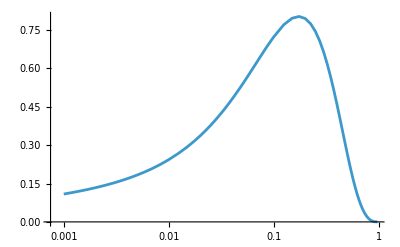

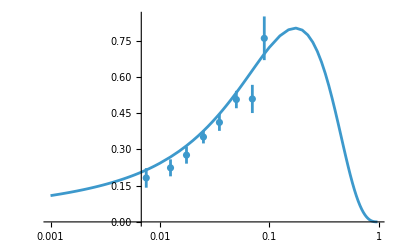

```mathematica
Needs["ErrorBarLogPlots`"]
g1=F3/.Q->20/.f->4;
twoN=8;
prec=70;

NInverseLaplaceTransformBlock[g1,s,v,twoN,prec]:=Module[{Omega,Alpha,M,p,den,r,num},(M=2*Ceiling[twoN/2];p=PadeApproximant[Exp[z],{z,0,{M-1,M}}];
den=Denominator[p];r=Roots[den==0,z];Alpha=Table[r[[i,2]],{i,1,M}];
num=Numerator[p];hospital=num/D[den,z];
Omega=SetPrecision[Table[hospital/.z->Alpha[[i]],{i,1,M,2}],prec+50];
Alpha=SetPrecision[Table[Alpha[[i]],{i,1,M,2}],prec]);
SetPrecision[-(2/v)Sum[Re[Omega[[i]] g1/.s->Alpha[[i]]/v],{i,1,M/2}],30]]

Parallelize[Table[{xx, Re[NInverseLaplaceTransformBlock[g1,s,v,twoN,prec]]/.v->Log[1/xx]},{xx,0.001,0.009,0.00025}]];
Parallelize[Table[{xx, Re[NInverseLaplaceTransformBlock[g1,s,v,twoN,prec]]/.v->Log[1/xx]},{xx,0.01,0.09,0.0025}]];
Parallelize[Table[{xx,  Re[NInverseLaplaceTransformBlock[g1,s,v,twoN,prec]]/.v->Log[1/xx]},{xx,0.1,0.99,0.025}]];
Join[%%%,%%,%]
xf3laplace=ListLogLinearPlot[%,Joined->True]
xf3Q20={{0.0075,0.1821,0.04039},{0.0125,0.2239,0.03512},{0.0175,0.2767,0.03549},{0.025,0.3517,0.0267},{0.035,0.4121,0.035},{0.05,0.5068,0.036},{0.07,0.5093,0.05839},{0.09,0.7605,0.09046}};
ErrorListLogLinearPlot[xf3Q20];
Show[%,xf3laplace,PlotRange->All]
```

```mathematica
Needs["ErrorBarLogPlots`"]
x=.
Nmax=.
Nmax=9;
α=3;
β=0.5;
θ=√((k!(2  k+α+β+1) Gamma[k+α+β+1])/(Gamma[k+α+1]Gamma[k+β+1]))(-1)^k/(k!x^β(1-x)^α)D[(x^(β+k)(1-x)^(α+k)), {x,k}];
ckj=√((k! (2 k+α+β+1) Gamma[k+α+β+1])/(Gamma[k+α+1]Gamma[k+β+1]))(-1)^k/(k!)1/(j!)(Pochhammer[-k,j]Pochhammer[α+β+k+1,j]Pochhammer[β+j+1,k-j]);Momentg1NLOxF3=(F3)/.s->j+1;

aαβ[k_]:=∑_(j=0)^k ckj*Momentg1NLOxF3;

xF3xQ=x^β(1-x)^α*(∑_(k=0)^Nmax θ*aαβ[k]);
```

```mathematica
xF3xQ/.f->3/.Q->2/.x->0.1
```

0.737057

```mathematica
NIntegrate[xF3xQ/x/.f->4/.Q->3,{x,0,1}]
```

2.73407

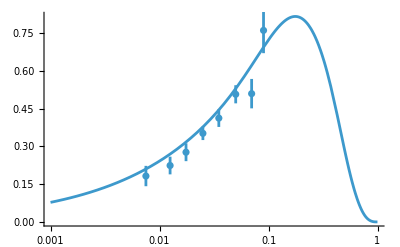

```mathematica
Needs["ErrorBarLogPlots`"]
xf3Q20={{0.0075,0.1821,0.04039},{0.0125,0.2239,0.03512},{0.0175,0.2767,0.03549},{0.025,0.3517,0.0267},{0.035,0.4121,0.035},{0.05,0.5068,0.036},{0.07,0.5093,0.05839},{0.09,0.7605,0.09046}};
ErrorListLogLinearPlot[xf3Q20];
LogLinearPlot[xF3xQ/.f->3/.Q->20,{x,0.001,0.999}];
Show[%,%%]
```

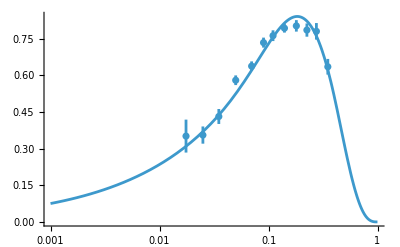

```mathematica
Needs["ErrorBarLogPlots`"]
xf3Q7p9={{0.0175,0.3513,0.06743},{0.025,0.3555,0.03521},{0.035,0.4316,0.03064},{0.05,0.58,0.01979},{0.07,0.6377,0.01946},{0.09,0.734,0.02048},{0.11,0.7624,0.022},{0.14,0.7931,0.01804},{0.18,0.8026,0.02349},{0.225,0.7854,0.0271},{0.275,0.7803,0.03387},{0.35,0.6352,0.03202}};
ErrorListLogLinearPlot[xf3Q7p9];
LogLinearPlot[xF3xQ/.f->4/.Q->7.9,{x,0.001,0.999}];
Show[%,%%]
```

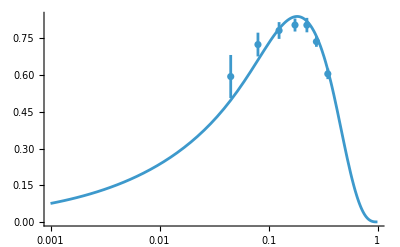

```mathematica
xf3Q8p155={{0.045,0.5941,0.08812945},{0.08,0.7249,0.048568405},{0.125,0.7823,0.03428644},{0.175,0.8047,0.026575365},{0.225,0.8044,0.029471681},{0.275,0.7368,0.02116034},{0.35,0.6051,0.0215}};
ErrorListLogLinearPlot[xf3Q8p155];
LogLinearPlot[xF3xQ/.f->4/.Q->8.155,{x,0.001,0.999}];
Show[%,%%]
```

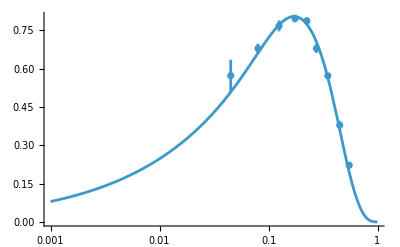

```mathematica
xf3Q19p952={{0.045,0.5729,0.062181669},{0.08,0.679,0.018713899},{0.125,0.7677,0.021220038},{0.175,0.7962,0.014817557},{0.225,0.7871,0.014024265},{0.275,0.6791,0.017284965},{0.35,0.5721,0.011203571},{0.45,0.3787,0.016790771},{0.55,0.2219,0.012518786}};
ErrorListLogLinearPlot[xf3Q19p952];
LogLinearPlot[xF3xQ/.f->4/.Q->19.952,{x,0.001,0.999}];
Show[%,%%]
```

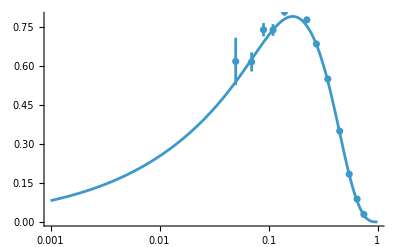

```mathematica
xf3Q31p6={{0.05,0.6167,0.09101},{0.07,0.6147,0.03683},{0.09,0.7384,0.02551},{0.11,0.7374,0.02253},{0.14,0.8071,0.01419},{0.18,0.828,0.01303},{0.225,0.7763,0.01066},{0.275,0.6839,0.01017},{0.35,0.549,0.006821},{0.45,0.3487,0.006094},{0.55,0.1834,0.005175},{0.65,0.08762,0.003702},{0.75,0.02875,0.002163}};
ErrorListLogLinearPlot[xf3Q31p6];
LogLinearPlot[xF3xQ/.f->4/.Q->31.6,{x,0.001,0.999}];
Show[%,%%]
```

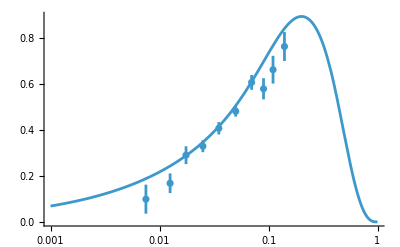

```mathematica
xf3Q3p2={{0.0075,0.09905,0.06319},{0.0125,0.1684,0.0429},{0.0175,0.2906,0.03887},{0.025,0.3298,0.02605},{0.035,0.4078,0.02699},{0.05,0.4822,0.02357},{0.07,0.6078,0.03228},{0.09,0.5799,0.04613},{0.11,0.663,0.06051},{0.14,0.7642,0.06294}};
ErrorListLogLinearPlot[xf3Q3p2];
LogLinearPlot[xF3xQ/.f->3/.Q->3.2,{x,0.001,0.999}];
Show[%,%%]
```

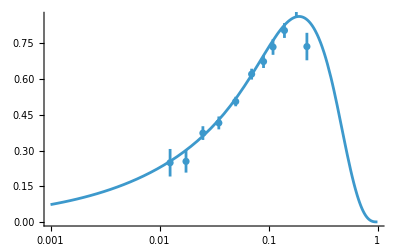

```mathematica
xf3Q5={{0.0125,0.2486,0.05783},{0.0175,0.2543,0.04715},{0.025,0.3732,0.02882},{0.035,0.4159,0.02706},{0.05,0.5058,0.01989},{0.07,0.6209,0.0228},{0.09,0.6738,0.02707},{0.11,0.735,0.03292},{0.14,0.8043,0.0312},{0.18,0.9044,0.04342},{0.225,0.7368,0.05772}};
ErrorListLogLinearPlot[xf3Q5];
LogLinearPlot[xF3xQ/.f->4/.Q->5,{x,0.001,0.999}];
Show[%,%%]
```

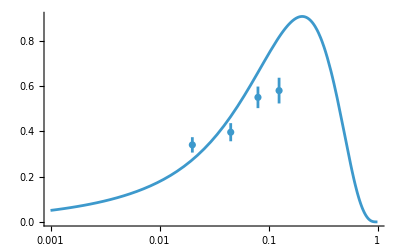

```mathematica
xf3datachorusQ2p052={{0.02,0.3398,0.033922854},{0.045,0.3957,0.04},{0.08,0.5495,0.047590335},{0.125,0.5793,0.056741607}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->3/.Q->2.052,{x,0.001,0.999}];
Show[%,%%]
```

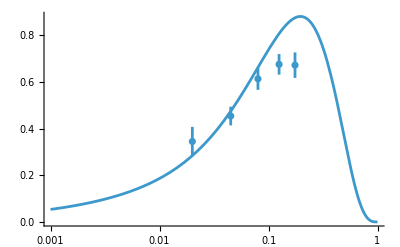

```mathematica
xf3datachorusQ3p25={{0.02,0.3448,0.062542466},{0.045,0.4539,0.040078049},{0.08,0.6133,0.047093524},{0.125,0.6755,0.043990567},{0.175,0.6721,0.054753265}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->3/.Q->3.25,{x,0.001,0.999}];
Show[%,%%]
```

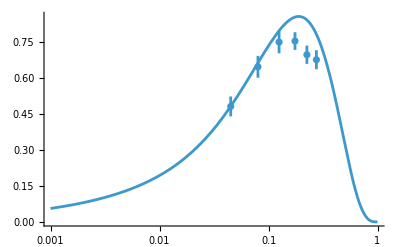

```mathematica
xf3datachorusQ5p146={{0.045,0.4823,0.04148795},{0.08,0.6478,0.045617979},{0.125,0.7509,0.046617164},{0.175,0.7554,0.036962819},{0.225,0.6982,0.038220544},{0.275,0.6773,0.0397}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->5.146,{x,0.001,0.999}];
Show[%,%%]
```

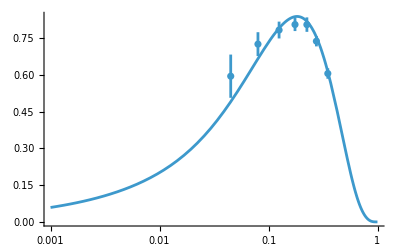

```mathematica
xf3datachorusQ8p155={{0.045,0.5941,0.08812945},{0.08,0.7249,0.048568405},{0.125,0.7823,0.03428644},{0.175,0.8047,0.026575365},{0.225,0.8044,0.029471681},{0.275,0.7368,0.02116034},{0.35,0.6051,0.0215}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->8.155,{x,0.001,0.999}];
Show[%,%%]
```

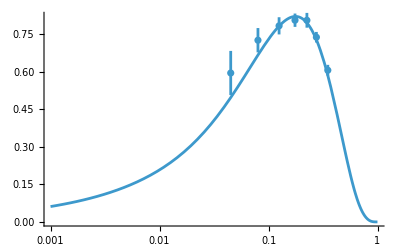

```mathematica
xf3datachorusQ12p925={{0.045,0.5941,0.08812945},{0.08,0.7249,0.048568405},{0.125,0.7823,0.03428644},{0.175,0.8047,0.026575365},{0.225,0.8044,0.029471681},{0.275,0.7368,0.02116034},{0.35,0.6051,0.0215}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->12.925,{x,0.001,0.999}];
Show[%,%%]
```

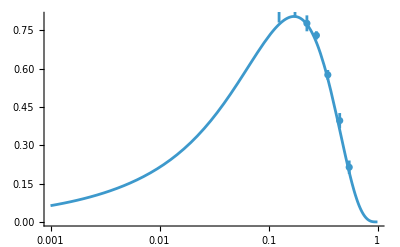

```mathematica
xf3datachorusQ20p52={{0.125,0.8431,0.063238754},{0.175,0.8352,0.03508903},{0.225,0.7768,0.031170018},{0.275,0.7297,0.016164467},{0.35,0.5753,0.019007893},{0.45,0.3962,0.02964473},{0.55,0.2138,0.026340273}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->20.52,{x,0.001,0.999}];
Show[%,%%]
```

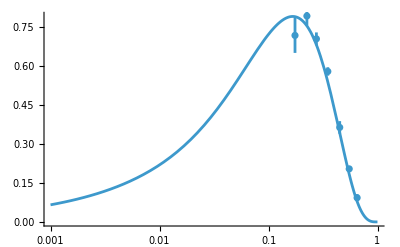

```mathematica
xf3datachorusQ32p5={{0.175,0.7165,0.067128012},{0.225,0.7911,0.036565831},{0.275,0.7034,0.024644675},{0.35,0.5781,0.016124515},{0.45,0.363,0.024223129},{0.55,0.2038,0.01077033},{0.65,0.0928,0.013703284}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->32.5,{x,0.001,0.999}];
Show[%,%%]
```

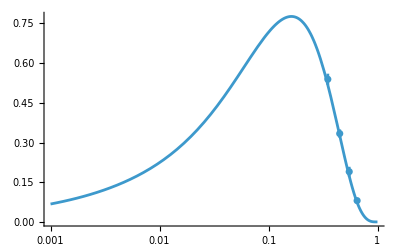

```mathematica
xf3datachorusQ51p455={{0.35,0.5391,0.021023796},{0.45,0.3338,0.015809491},{0.55,0.1898,0.0185},{0.65,0.0803,0.010469479}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->51.455,{x,0.001,0.999}];
Show[%,%%]
```

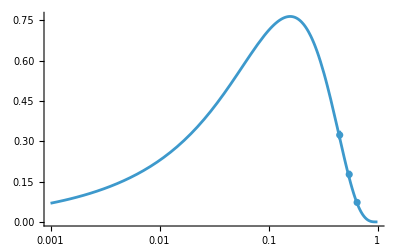

```mathematica
xf3datachorusQ81p55={{0.45,0.3234,0.015929846},{0.55,0.1767,0.013780058},{0.65,0.0725,0.0086539}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->81.55,{x,0.001,0.999}];
Show[%,%%]
```

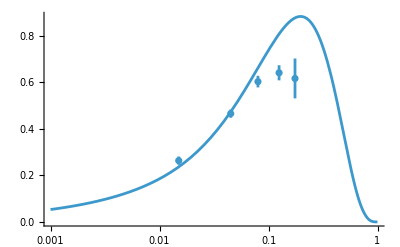

```mathematica
xf3dataNuTeVQ3p162={{0.015,0.2634,0.017717788},{0.045,0.4655,0.017713554},{0.08,0.6031,0.024899799},{0.125,0.641,0.032422986},{0.175,0.6167,0.085731091}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->3.162,{x,0.001,0.999}];
Show[%,%%]
```

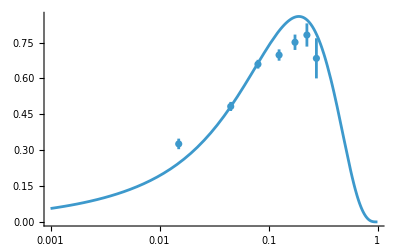

```mathematica
xf3dataNuTeVQ5p012={{0.015,0.3262,0.022040871},{0.045,0.4829,0.018944392},{0.08,0.6596,0.018292621},{0.125,0.698,0.023652695},{0.175,0.7514,0.032137828},{0.225,0.7818,0.048489277},{0.275,0.6842,0.083944982}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->5.012,{x,0.001,0.999}];
Show[%,%%]
```

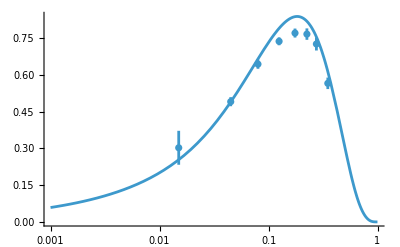

```mathematica
xf3dataNuTeVQ7p943={{0.015,0.3026,0.0692943},{0.045,0.4908,0.018509727},{0.08,0.6441,0.018894973},{0.125,0.7373,0.016118002},{0.175,0.771,0.018348024},{0.225,0.7667,0.02330751},{0.275,0.7264,0.026644699},{0.35,0.5658,0.023479566}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->7.943,{x,0.001,0.999}];
Show[%,%%]
```

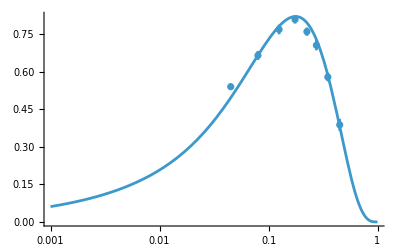

```mathematica
xf3dataNuTeVQ12p589={{0.045,0.54,0.012608331},{0.08,0.6651,0.017859451},{0.125,0.7687,0.019229405},{0.175,0.8087,0.016442932},{0.225,0.76,0.01653844},{0.275,0.7057,0.020111191},{0.35,0.5789,0.017388789},{0.45,0.3878,0.02367467}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->12.589,{x,0.001,0.999}];
Show[%,%%]
```

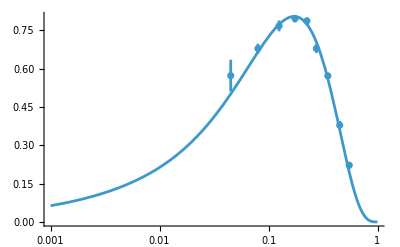

```mathematica
xf3dataNuTeVQ19p952={{0.045,0.5729,0.062181669},{0.08,0.679,0.018713899},{0.125,0.7677,0.021220038},{0.175,0.7962,0.014817557},{0.225,0.7871,0.014024265},{0.275,0.6791,0.017284965},{0.35,0.5721,0.011203571},{0.45,0.3787,0.016790771},{0.55,0.2219,0.012518786}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->19.952,{x,0.001,0.999}];
Show[%,%%]
```

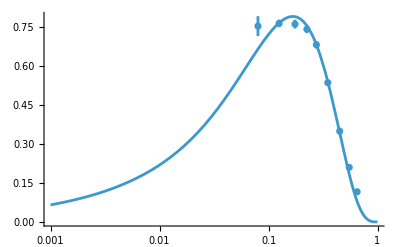

```mathematica
xf3dataNuTeVQ31p622={{0.08,0.7531,0.038191884},{0.125,0.7634,0.0145},{0.175,0.7608,0.017046407},{0.225,0.7413,0.015138692},{0.275,0.6812,0.01385785},{0.35,0.5355,0.009053729},{0.45,0.3489,0.012938315},{0.55,0.2097,0.008013738},{0.65,0.1158,0.007993748}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->31.622,{x,0.001,0.999}];
Show[%,%%]
```

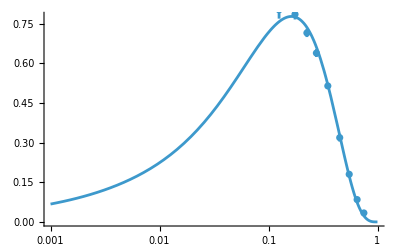

```mathematica
xf3dataNuTeVQ50p118={{0.125,0.8024,0.03345355},{0.175,0.7853,0.019519221},{0.225,0.7149,0.015636496},{0.275,0.6387,0.014903355},{0.35,0.5144,0.010024969},{0.45,0.3187,0.014701701},{0.55,0.1801,0.010396153},{0.65,0.0844,0.006878227},{0.75,0.0338,0.004890808}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->50.118,{x,0.001,0.999}];
Show[%,%%]
```

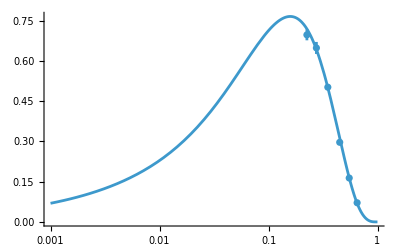

```mathematica
xf3dataNuTeVQ79p432={{0.225,0.6968,0.020329535},{0.275,0.648,0.022387497},{0.35,0.5018,0.008210968},{0.45,0.2965,0.008000625},{0.55,0.1635,0.006745369},{0.65,0.0713,0.006289674}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->79.432,{x,0.001,0.999}];
Show[%,%%]
```

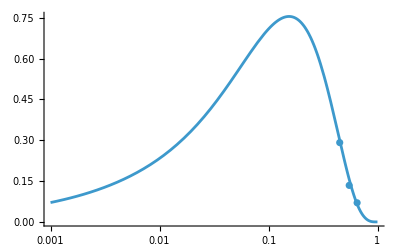

```mathematica
xf3dataNuTeVQ125p89={{0.45,0.2913,0.010435037},{0.55,0.1341,0.01007075},{0.65,0.0702,0.008610459}};
ErrorListLogLinearPlot[%];
LogLinearPlot[xF3xQ/.f->4/.Q->125.89,{x,0.001,0.999}];
Show[%,%%]
```

```mathematica
NIntegrate[xF3xQ/x/.f->4/.Q->8,{x,0,1}]
```

2.56306

```mathematica
ZZ=26;
NN=30;
AA=56;
(ZZ-NN)/AA//N
```

-0.0714286